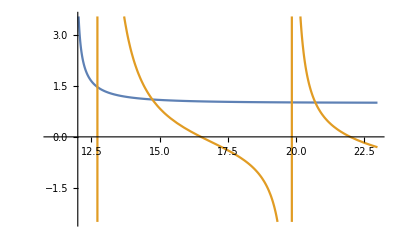

```mathematica
Clear[beta];
k=2*N[Pi]; n1=1.5;n2=1.9;n3=3.6;n4=1.5;d=0.06;H=0.25;
K1=Sqrt[beta^2-k^2*n1^2];K2=Sqrt[beta^2-k^2*n2^2];
K3=Sqrt[-beta^2+k^2*n3^2];K4=Sqrt[beta^2-k^2*n4^2];
f1[beta_]:=(K1*Cosh[K2*d]+K2*Sinh[K2*d])/(K2*Cosh[K2*d]+K1*Sinh[K2*d]);
f2[beta_]:=-K3/K2*(K4*Cos[K3*H]-K3*Sin[K3*H])/(K3*Cos[K2*H]+K4*Sin[K3*H]);
Plot[{f1[beta],f2[beta]},{beta,11,23}]
```

```mathematica
FindRoot[f1[beta]-f2[beta]==0,{beta,15.5}]
```

{beta→14.7368}

```mathematica
FindRoot[f1[beta]-f2[beta]==0,{beta,20.7}]
```

{beta→20.7258}

```mathematica
beta=14.7368;d=0.06;H=0.25;k=2*N[Pi]; n1=1.5;n2=1.9;n3=3.6;n4=1.5;K1=Sqrt[beta^2-k^2*n1^2];K2=Sqrt[beta^2-k^2*n2^2];
K3=Sqrt[-beta^2+k^2*n3^2];K4=Sqrt[beta^2-k^2*n4^2];
B=-(K2*Cosh[K2*d]+K1*Sinh[K2*d])/(K1*Cosh[K2*d]+K2*Sinh[K2*d]);
A=B*Cosh[K2*d]+Sinh[K2*d];
EE=K2/K3;
F=B*Cos[K3*H]-K2*Sin[K3*H]/K3;
f3=Integrate[(B*Cosh[K2*x]+Sinh[K2*x])^2,{x,0,d}];
f4=Integrate[(B*Cos[K3*x]+EE*Sin[K3*x])^2,{x,-H,0}];
gamma=f3/(f3+f4+A^2/(2*K1)+F^2/(2*K4));
gamma2=f4/(f3+f4+A^2/(2*K1)+F^2/(2*K4))
```

0.699336

```mathematica
gamma
```

0.12424

```mathematica
beta=20.7258;d=0.06;H=0.3;k=2*N[Pi]; n1=1.5;n2=1.9;n3=3.6;n4=1.5;K1=Sqrt[beta^2-k^2*n1^2];K2=Sqrt[beta^2-k^2*n2^2];
K3=Sqrt[-beta^2+k^2*n3^2];K4=Sqrt[beta^2-k^2*n4^2];
B=-(K2*Cosh[K2*d]+K1*Sinh[K2*d])/(K1*Cosh[K2*d]+K2*Sinh[K2*d]);
A=B*Cosh[K2*d]+Sinh[K2*d];
EE=K2/K3;
F=B*Cos[K3*H]-K2*Sin[K3*H]/K3;
f3=Integrate[(B*Cosh[K2*x]+Sinh[K2*x])^2,{x,0,d}];
f4=Integrate[(B*Cos[K3*x]+EE*Sin[K3*x])^2,{x,-H,0}];
gamma=f3/(f3+f4+A^2/(2*K1)+F^2/(2*K4));
gamma2=f4/(f3+f4+A^2/(2*K1)+F^2/(2*K4))
```

0.963886

```mathematica
gamma
```

0.0314204